```mathematica
Manipulate[

Show[

RegionPlot[ImplicitRegion[x^2+y^2<r^2&&(x-0.5)^2/(δ/2)^2+(y)^2/(((√(δ^2-1))/2)^2)<1,{x,y}],PlotRange->{{-0.5,1.5},{-1,1}}],
Graphics[{
{PointSize[0.015],Point[{0,0}]},
{PointSize[0.015],Point[{1,0}]},
Circle[{0,0},r],
Circle[{1/2,0},{δ/2,(√(δ^2-1))/2}]
}]]
,{{r,0.1},0.01,2,0.01},{{δ,1.5},1,2}]
```

```mathematica
temp=FindRoot[0.7*Cos[ϕ]-0.5,{ϕ,0.1}][[1]];
sol=(ϕ/.temp);
```

ϕ→0.775193

0.775193

```mathematica
Plot[Area[ImplicitRegion[x^2+y^2<r^2&&(x-0.5)^2/(δ/2)^2+(y)^2/(((√(δ^2-1))/2)^2)<1,{x,y}]],{r,0,2}]
```

$Aborted

```mathematica
data=With[{δ=2},Table[{r,Area[ImplicitRegion[x^2+y^2<r^2&&(x-0.5)^2/(δ/2)^2+(y)^2/(((√(δ^2-1))/2)^2)<1,{x,y}]]},{r,0,2,0.001}]];
```

```mathematica
diffdata=Table[{0.001*k,(data[[k+1,2]]-data[[k,2]])/0.001},{k,1,2000}];
```

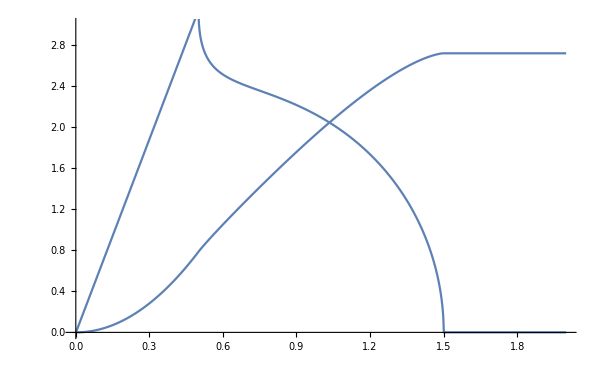

```mathematica
Show[ListLinePlot[data],ListLinePlot[diffdata],PlotRange->{{0,2},{0,3}},ImageSize->600]
```

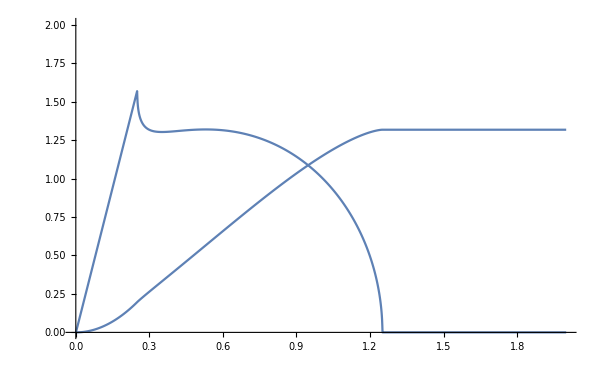

```mathematica
Show[ListLinePlot[data],ListLinePlot[diffdata],PlotRange->{{0,2},{0,2}},ImageSize->600]
```